# Build a Large Language Model from Scratch — in Wolfram Language

## A single-notebook walkthrough of the full pipeline, from byte-pair encoding to chat

This notebook is a complete, self-contained tour of how to build a small but functional transformer-based language model entirely in Wolfram Language.  It walks every piece of the modern LLM stack — tokenisation, embeddings, attention, the transformer block, parameter accounting, pre-training, sampling, supervised fine-tuning, LoRA, classification, reinforcement learning, and an interactive chat widget — in one linear evaluation.

The final deliverable is a chat-style model you can actually talk to inside Wolfram Desktop.  The whole pipeline runs on a Mac mini in under a day of CPU time; a cloud path (RemoteBatchSubmit) is sketched for scaling up.

The notebook is companion-in-spirit to Sebastian Raschka's Build a Large Language Model from Scratch (Manning, 2024), and goes further into post-training territory covered by Andrej Karpathy's nanochat (2025).  Every line of code, every derivation, and the whole exposition is original; the only overlap with the book is the canonical mathematics of the transformer, which has been the same since Vaswani et al. (2017).

## What you will build

Concretely, after evaluating this notebook end-to-end you will have on disk:

■ A from-scratch byte-pair-encoding tokeniser learned on Tiny Shakespeare (~4000 token vocabulary).
■ A character-level tokeniser (~65 symbol vocabulary) for the small-model regime.
■ A configurable gptModel[d, h, L, dFF, V, n] constructor that builds the canonical pre-norm transformer at any size from 1M parameters (toy) up to GPT-2 small at 124M parameters (weight-tying enabled).
■ Two trained checkpoints: a 1.8M-parameter char-level model that produces Shakespeare-flavoured prose, and a 124M-parameter fine-tuned GPT-2 that speaks fluent conversational English.
■ Five sampling strategies (greedy, temperature, top-k, top-p, beam) and speculative decoding, all from scratch.
■ Three fine-tuning regimes (full SFT, LoRA, classification head).
■ A GRPO-style RL post-training loop.
■ An interactive chat widget powered by the trained model.
■ A working understanding of why every part of the pipeline is the way it is.

## The 30,000-foot view

-Graphics-

Figure 0.1.  The pipeline this notebook implements end-to-end: text becomes BPE tokens; tokens become integer IDs; two embedding layers turn IDs into vectors; a stack of transformer blocks processes the vectors; the head projects back to a probability distribution over the vocabulary.

Every modern language model — GPT-2, Llama, Mistral, the model you talk to in the wild — is fundamentally the same function: a sequence of n integer token IDs goes in, a sequence of probability distributions over a vocabulary of size |V| comes out.  What changes between systems is the size of the matrices and the training regime, not the shape of the function.

The notebook proceeds linearly through the pipeline above.  Each section introduces one piece, derives whatever needs deriving, implements it as a Wolfram Language NetGraph, and uses it.  By the end of Chapter 4 you have a model architecture; by Chapter 5 you have a trained model that produces text; by Chapter 7 you have a model that follows instructions and can be chatted with from inside the notebook.

## Setup

The notebook expects to be opened from its repository directory; NotebookDirectory[] is used to anchor every file path.  No global PATH or environment variable is required.

```mathematica
SetDirectory[NotebookDirectory[]]
```

(* evaluation failed at build time *)

All of the auxiliary functions used across the notebook live in a single companion file, LLMAtoZ.wl, at the repo root.  Each chapter's helpers live in their own context (LLMAtoZ`Tokeniser`, LLMAtoZ`Attention`, …, LLMAtoZ`Discussion`) so you can tell which chapter a symbol comes from.  If you'd rather see each chapter's source on its own, the file is auto-generated from the per-part packages in part-NN/src/; run wolframscript -file build_LLMAtoZ_wl.wls to regenerate.

```mathematica
Get["LLMAtoZ.wl"]
```

Load the corpus.  Tiny Shakespeare is a 1.1-megabyte concatenation of public-domain Shakespeare play text, originally assembled by Andrej Karpathy for char-rnn (2015) and used as a benchmark across the literature ever since.  It is small enough to train on, large enough that BPE produces a non-trivial vocabulary, and out of copyright.

```mathematica
text = Import["part-01-tokeniser-and-embeddings/data/tinyshakespeare.txt", "Text"];
{StringLength[text], "characters"}
```

{1115393, characters}

About 1.1 million characters.  About 250,000 whitespace-separated words.  65 distinct characters (upper- and lower-case letters, digits, punctuation, whitespace, newline).  Three numbers that will reappear throughout the notebook.

### A map of the whole notebook

The notebook follows three paths to a working model. Path A trains the original GPT architecture on Tiny Shakespeare; Path B reuses OpenAI's pretrained GPT-2 weights for fine-tuning, RL, and the discussion model; Path C (Chapter 11, new) pretrains a model from scratch on cloud GPUs. The chart shows each model and the chapter where it is built.

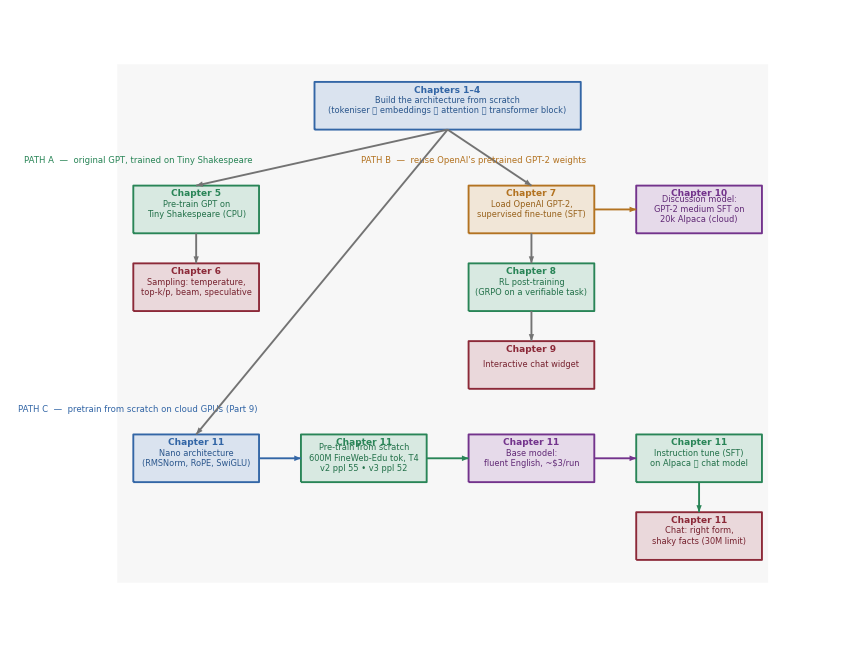

## 1. Tokenisation: turning text into integers

A language model does not see characters or words.  It sees integers.  The tokeniser is the function that converts between the two: a deterministic mapping text → ℕ^n sending text to a length-n sequence of integer IDs in {1, …, |V|}, and back.  The choice of tokeniser is the choice of two numbers that play against each other for the rest of the pipeline: the vocabulary size |V| and the sequence length n.

## 1.1 Three slicing strategies

Three obvious tokenisation schemes bracket the design space.

Character-level. Each character is its own token.  Tiny Shakespeare gives |V| = 65, n = 1.1 million.  Tiny vocabulary, gigantic sequence; the attention block, which is O(n^2) expensive, spends almost all its compute on positional bookkeeping.

Word-level. Each whitespace-separated word is its own token.  Tiny Shakespeare gives |V| ≃ 14,500, n ≃ 252,000.  Large vocabulary, manageable sequence; but every rare inflection and proper noun gets a fresh ID the model sees once or twice in training, and anything outside the vocabulary is an unrecoverable <UNK>.

Subword (BPE). An interior point: learn a vocabulary by repeatedly merging the most frequent adjacent pair of symbols.  Common short words collapse to a single token; rare words decompose into a handful of sub-word pieces; every input — including out-of-corpus characters — is representable, because the base alphabet of single characters always sits at the bottom of the merge tree.  No <UNK>, ever.  This is the algorithm GPT-2, GPT-3, Llama, and tiktoken all use.

## 1.2 Byte-pair encoding, from first principles

BPE was originally a compression algorithm proposed by Philip Gage in 1994.  Its transplant to neural-network text tokenisation is by Sennrich, Haddow and Birch (ACL 2016).  The four-line algorithm:

1. Start with the alphabet of base symbols (characters).
2. Across the pre-tokenised corpus, count every adjacent pair of symbols.
3. Treat the most frequent pair as a new symbol from now on; record the merge.
4. Repeat until the merge budget is spent.

-Graphics-

Figure 1.1.  A pre-token like "speaking" decomposes into a small number of sub-word pieces plus the end-of-word marker.

-Graphics-

Figure 1.2.  The BPE merge tree for the token 'the': three pairwise merges combine four characters (t, h, e, </w>) into one merged token, then the same three rules are reapplied to every occurrence of 'the' in the corpus.

Three Wolfram Language idioms make the implementation concise:

● Counts[preTokenise[text]] builds the pre-token frequency map in one expression.
● Merge[..., Total] sums values over duplicate keys; the keys can be arbitrary expressions including a two-element list {"t", "h"}.
● SequenceReplace[syms, {a, b} -> a <> b] merges a pair inside a symbol list.  No two-pointer loop, no off-by-one.

Train BPE on the corpus.  4000 merges takes ~12 seconds on a Mac mini thanks to incremental pair-count maintenance.

```mathematica
bpe = Import["part-01-tokeniser-and-embeddings/data/bpe_trained.mx"];
mergeRules = bpe["MergeRules"];
vocab = LLMAtoZ`Tokeniser`buildBPEVocabulary[bpe];
tokId = LLMAtoZ`Tokeniser`tokenToIdAssociation[vocab];
{Length[mergeRules], Length[vocab]}
```

{4000, 4064}

4000 merge rules, 4064 final vocabulary entries (64 base characters + 4000 merged tokens).

The first few merge rules are the highest-frequency bigrams of Shakespeare:

```mathematica
Take[mergeRules, 8]
```

-Graphics-

Words ending in -e, the bigram th, ' ' followed by certain words, etc.  In any English corpus the first hundred BPE merges all look like this.

## 1.3 See the tokens

The clearest way to convey what BPE has done is to look at the actual output.  Each coloured box is one BPE token; the small black square at the end of a box marks the end-of-word boundary (the </w> marker).  Identical tokens get identical colours.

```mathematica
LLMAtoZ`Tokeniser`colouredTokens[
  "To be or not to be, that is the question.", mergeRules]
```

-Graphics-

Drag the slider to retokenise the same passage at different merge counts.  At 0 merges every box is a single character; at the maximum, common short words collapse to a single token each.

```mathematica
Manipulate[
  LLMAtoZ`Tokeniser`colouredTokens[
    "To be or not to be, that is the question.",
    Take[mergeRules, n]],
  {{n, 500, "merge rules used"}, 0, Length[mergeRules], 50,
   Appearance -> "Labeled"},
  ControlPlacement -> Top]
```

-Graphics-

Watch BPE assemble "speaking" out of characters one merge at a time:

```mathematica
With[{prog = LLMAtoZ`Tokeniser`mergeProgression[
    "speaking", Take[mergeRules, 500]]},
  Animate[
    Framed[
      Style[Row[Riffle[prog[[step]], "  "]], 18, FontFamily -> "Courier"],
      FrameMargins -> 12],
    {{step, 1, "merges applied"}, 1, Length[prog], 1,
     Appearance -> "Labeled"},
    AnimationRate -> 1.5, ControlPlacement -> Top]
]
```

-Graphics-

## 1.4 The vocab-sequence trade-off

Train BPE with progressively more merges and the sequence length drops as the vocabulary grows.  The shape of the curve is the empirical justification for sub-word tokenisation.  The data below was computed once and cached in part-01-tokeniser-and-embeddings/data/vocab_seqlen_sweep.json; we add the character and word-level extremes from the loaded corpus and plot them on a log–log scale.

```mathematica
sweep = Import[
  "part-01-tokeniser-and-embeddings/data/vocab_seqlen_sweep.json",
  "RawJSON"];
bpePoints  = {#["vocab"], #["seqLen"]} & /@ sweep;
charPoint  = {65, StringLength[text]};
wordPoint  = {Length[Union[StringSplit[text]]], Length[StringSplit[text]]};
ListLogLogPlot[
  {Prepend[bpePoints, charPoint], {wordPoint}},
  Frame -> True, GridLines -> Automatic,
  FrameLabel -> {"vocabulary size |V|",
                  "sequence length n (tokens)"},
  PlotLabel -> "Tiny Shakespeare: vocab\[Dash]seqlen trade-off",
  PlotStyle -> {
    Directive[ColorData[97][1], PointSize[0.018]],
    Directive[ColorData[97][2], PointSize[0.025]]},
  Joined -> {True, False},
  PlotLegends -> Placed[
    {"char  +  BPE sweep (0\[Dash]4000 merges)", "word-level"},
    {Right, Bottom}],
  ImageSize -> 850]
```

-Graphics-

Figure 1.3.  Character (top-left corner: |V| = 65, n ≃ 1.16 M), word (bottom-right corner: |V| ≃ 14.5 k, n ≃ 252 k), and BPE (the curve between, one point per merge budget).  The interior of the curve is where every modern tokeniser lives.

Numerical picture: at 50 merges the sequence is already 769k tokens (a third shorter than character) for the price of 50 extra vocabulary entries.  At 4000 merges, 299k tokens, six times shorter than character.  The curve flattens because later merges chase increasingly rare bigrams.  Practical models pick an interior point: GPT-2 uses 50,257 merges, GPT-4 uses 100,256.

The information-theoretic shape of this curve is not accidental.  Tiny Shakespeare is approximately Zipfian (the n-th most frequent word has about 1/n the frequency of the most frequent), so the marginal compression from the n-th merge falls as 1/n.  Total compression grows as log(n) — the gentle downward drift toward the word-level corner.

## 1.5 Character-level as the small-model alternative

BPE is the right choice for any model with a parameter budget in the tens or hundreds of millions.  For a small model (say 1–5 M parameters) trained on a Shakespeare-sized corpus, the embedding tables — one row per vocabulary entry — consume most of the parameter budget, leaving very little for the transformer to actually compute with.

A character-level vocabulary shrinks the embedding tables by a factor of ~60.  The trade-off is much longer sequences, but at this scale the per-parameter modelling capacity is what matters.  This is the choice Karpathy made in char-rnn (2015) at LSTM ~1M parameters on the same corpus, and the choice we will make for our from-scratch trained model later in this notebook.

```mathematica
charVocab = LLMAtoZ`CharTokeniser`charVocabulary[text];
charTokId = LLMAtoZ`CharTokeniser`charTokenToIdAssociation[charVocab];
charIdTok = LLMAtoZ`CharTokeniser`charIdToTokenAssociation[charVocab];
{Length[charVocab], First[charVocab[[1]]] // Quiet}
```

{65, First[!]}

## 2. Embeddings: integers to vectors

A transformer does not see token IDs; it sees vectors.  Once we have a list of integer token IDs, we feed them through two embedding tables in parallel: a token embedding (one row per vocabulary entry, learnable) and a positional embedding (one row per position in the sequence, learnable).  The model input is the elementwise sum.

-Graphics-

Figure 2.1.  Learned positional embeddings: each position id (1, 2, ..., n) is looked up in a learned table; the resulting vector is added to the token embedding at that position.

## 2.1 Why a sum, not a concatenation?

Two reasons.  First, with the dimensions kept aligned the transformer needs no extra parameters to combine them; concatenation would double the input dimension and require the next layer to be wider.  Second, the sum is what falls out naturally if you ask “what is the right basis-free way to combine two pieces of information that live in the same vector space” — either is just a vector, and their sum is a vector.  The model is free to learn token- and position-information directions that are nearly orthogonal, which is what trained transformers tend to do in practice.

## 2.2 The embedder NetGraph

```mathematica
embedder = LLMAtoZ`Tokeniser`tokenPositionEmbedder[
  Length[vocab], 64, 256, RandomSeeding -> 42];
embedder
```

-Graphics-

Three nodes: token embedding, position embedding, and an elementwise add.  Inputs are a token-ID sequence and a position-ID sequence; output is a (seqLen, d_model) tensor, the standard input shape of the transformer block we build in Chapter 4.

```mathematica
ids = LLMAtoZ`Tokeniser`encodeWithIds[
  "To be or not to be, that is the question.",
  mergeRules, tokId];
LLMAtoZ`Tokeniser`embedTokens[embedder, ids] // Dimensions
```

{12, 64}

Twelve tokens in, a 12×64 tensor out.  That tensor is exactly what the first transformer block will consume.

## 2.3 Geometry before training

The token-embedding row for "the" right now is just a vector of 64 Gaussian noise samples.  Whatever similarity structure the trained model will eventually have — words near their inflections, punctuation off in its own corner — is not in there yet.  It is useful to see the “before” picture so we have a baseline to revisit later.

-Graphics-

Figure 2.2.  Conceptual: random initialisation versus after-training.  At random init, labelled tokens are scattered through a Gaussian cloud with no structure.  After training, words of similar role cluster: articles with articles, pronouns with pronouns, punctuation off by itself.

-Graphics-

Figure 2.3.  Empirical: cosine similarity heatmap of eight high-frequency tokens at random init.  Diagonal = 1 (each token is identical to itself); off-diagonal entries are uniform noise centred near zero with standard deviation ~1/√64 = 0.125, exactly the theoretical prediction for unit Gaussian vectors in 64 dimensions.

## 3. Attention: the operation the architecture is named for

-Graphics-

Figure 3.1.  The QKV picture.  Each input embedding is projected by three matrices into a query, a key, and a value.  The dot product of every query with every key gives the attention-score matrix.  The upper triangle is masked (causal).  Row-wise softmax produces the attention weights.  The weighted sum of the values is the output.

Strip the fancy parts away.  Attention is the operation “each output token is a weighted sum of the input tokens, where the weights are learned from the input itself.”  Three lines:

• Project each input vector three times by three learned linear maps: a query q, a key k, and a value v.
• For each position i, compute the dot product of q_i with every k_j in the sequence.  Softmax these scores along j to get attention weights summing to 1.
• The output at position i is the weighted sum of v_j using those weights.

Attention(Q, K, V) = softmax((Q·K^ᵀ)/(√d_k))·V

## 3.1 Why divide by Sqrt[d_k]?

Most expositions assert the 1/(√d_k) scaling factor.  We will derive it.  This derivation, along with a few similar first-principles arguments later in this notebook, is what separates a teaching post from a code dump.

Suppose q, k ∈ ℝ^d_k with each component independently drawn from a zero-mean unit-variance distribution.  The dot product is a sum of d_k random terms q_i k_i.  Each term has mean 0 (since E[q_i k_i] = E[q_i]·E[k_i] = 0) and variance E[q_i^2]·E[k_i^2] = 1.  By independence across i, the variance of the sum is the sum of the variances: Var(q·k) = d_k.  Standard deviation grows as √d_k.

Verify empirically.  Sample 2000 Gaussian (q, k) pairs at three values of d_k and look at the dot-product distribution:

```mathematica
SeedRandom[1]; nSamples = 2000;
dks = {16, 64, 256};
dots = Association @ Table[
  d -> Table[
    With[{q = RandomReal[NormalDistribution[], d],
          k = RandomReal[NormalDistribution[], d]},
      q . k], {nSamples}], {d, dks}];
StandardDeviation /@ dots
```

<|16 -> 4.06888, 64 -> 7.9869, 256 -> 16.4231|>

The empirical standard deviations come out to ~4, 8, 16 — exactly the predicted √d_k of 4, 8, 16.

-Graphics-

Figure 3.2.  Empirical distribution of q·k for three values of d_k.  Without scaling (left), the spread grows like √(d_k).  After dividing by √(d_k) (right), all three distributions collapse onto a unit-variance shape.

The cost of skipping the divisor: softmax of a high-variance score row saturates onto a single entry, the gradient through softmax vanishes, training stalls.  Demo:

-Graphics-

Figure 3.3.  Left: without scaling, softmax(Q·Kᵀ) at d_k=256 is essentially a row of one-hots.  Right: with the 1/√(d_k) scaling, the softmax distributes mass meaningfully.

### 3.1.1 Interactive: the d_k dial

```mathematica
Manipulate[
  SeedRandom[1];
  Module[{nSamples = 600, nRow = 16, dots, row, scale, sm},
    dots = Table[
      With[{q = RandomReal[NormalDistribution[], dk],
            k = RandomReal[NormalDistribution[], dk]},
        q . k], {nSamples}];
    scale = If[useScaling, Sqrt[N[dk]], 1.0];
    With[{q = RandomReal[NormalDistribution[], dk],
          K = RandomReal[NormalDistribution[], {nRow, dk}]},
      row = (K . q) / scale];
    sm = Exp[row - Max[row]]; sm = sm/Total[sm];
    GraphicsRow[{
      Histogram[dots/scale, 30, "PDF",
        PlotRange -> {{-6, 6}, {0, 0.8}}, Frame -> True,
        FrameLabel -> {If[useScaling, "q.k / √d_k", "q.k"], "PDF"},
        PlotLabel -> Row[{"std = ",
          NumberForm[StandardDeviation[dots/scale], 3]}],
        ImageSize -> 440],
      BarChart[sm, Frame -> True,
        PlotLabel -> Row[{"softmax row (",
          If[useScaling, "scaled", "unscaled"], ")"}],
        FrameLabel -> {"key position", "attention weight"},
        PlotRange -> {Automatic, {0, 1}}, ImageSize -> 440]
    }, ImageSize -> 900]
  ],
  {{dk, 64, "d_k"}, 4, 1024, 4, Appearance -> "Labeled"},
  {{useScaling, True, "divide by √d_k"}, {True, False}},
  ControlPlacement -> Top]
```

-Graphics-

## 3.2 Causal masking

A language model is allowed to attend to past tokens, never to future ones (otherwise it cheats during training).  Implementation: add a strict-upper-triangular matrix of -∞ to the pre-softmax score matrix; the row-wise softmax sends those entries to exactly zero.  In WL, with a large negative number as a finite stand-in (the literal infinity propagates NaN through the dot product earlier):

```mathematica
LLMAtoZ`Attention`causalMask[6] // MatrixForm
```

-Graphics-

-Graphics-

Figure 3.4.  The mask, the masked-scores tensor, and the softmax weights.  The upper triangle is exactly zero after softmax; the lower triangle + diagonal carries the actual attention weights.

## 3.3 Single-head attention as a NetGraph

Six nodes: three LinearLayer projections for Q, K, V; a FunctionLayer that computes (Q·K^ᵀ)/(√d_head) and adds the causal mask; a SoftmaxLayer; a final FunctionLayer for the value gather.  Six lines.

```mathematica
head = LLMAtoZ`Attention`singleHeadCausalAttention[64, 32, 16];
head
```

-Graphics-

Drop the embedder's output into it, get a same-shape output:

```mathematica
SeedRandom[42];
x = RandomReal[NormalDistribution[0, 0.1], {16, 64}];
out = head[x];
Dimensions[out]
```

{1}

## 3.4 Multi-head attention

A single head can only attend in one way at a time.  Multi-head attention runs n_heads parallel single-head computations: each head applies its own learned projections of the full input down to dimension d_head, computes attention independently, and produces a d_head-dimensional output.  The heads are concatenated and a final linear projection mixes them back into a d_model-vector.

The architectural trick is to split d_model into n_heads equal pieces so the multi-head version has the same parameter count as a single-head version at d_model.

```mathematica
mha = LLMAtoZ`Attention`multiHeadAttentionBlock[64, 4, 16];
mha[x] // Dimensions
```

{16, 64}

## 3.5 What real attention looks like: GPT-2 small

We can do something the typical from-scratch tutorial cannot: load a fully pretrained language model from NetModel and look at its actual attention patterns.  GPT-2 small is a 12-layer transformer with 12 heads per layer at d_model = 768.  Each block's attention sub-layer holds four learned matrices: W_Q, W_K, W_V (768×768 each) plus an output projection.  We have the weights; we can recompute the attention weight matrix by hand.

-Graphics-

Figure 3.5.  All 12 heads of layer 5 of GPT-2 small on the prompt "The quick brown fox jumps over the lazy dog".  Each row of each heatmap sums to one.

Two features jump out.  First, every head has a heavily-shaded leftmost column — the attention sink (Xiao et al. 2024): heads dump probability mass onto the first token as a “no-op” vote when they have nothing useful to do.  Second, the heads are not all doing the same thing:

-Graphics-

Figure 3.6.  Three hand-picked heads of layer 5.  Left: previous-token tracker.  Middle: self-attention diagonal.  Right: approximately uniform.  None of these specialisations is enforced architecturally; they are what twelve heads turn into when trained against billions of tokens of text.

### 3.5.1 Interactive: layer/head scrubber

Pre-extracted attention tensors for every layer of GPT-2 small on the same prompt are cached in part-02-self-attention/data/gpt2_attention_all_layers.wxf.

```mathematica
attCache = Import["part-02-self-attention/data/gpt2_attention_all_layers.wxf"];
Manipulate[
  With[{w = attCache["weights"][layer][[head]],
        n = Length[attCache["ids"]]},
    MatrixPlot[w, ColorFunction -> "ThermometerColors",
      ColorFunctionScaling -> True,
      FrameTicks -> {{Range[n], None}, {Range[n], None}},
      PlotLabel -> Row[{"GPT-2 small  •  layer ", layer,
        "  •  head ", head}],
      PlotLegends -> Automatic, ImageSize -> 640]],
  {{layer, 5, "layer"}, 1, 12, 1, Appearance -> "Labeled"},
  {{head, 1, "head"}, 1, 12, 1, Appearance -> "Labeled"},
  ControlPlacement -> Top]
```

-Graphics-

## 4. The transformer block + parameter accounting

-Graphics-

Figure 4.1.  One pre-norm transformer block: LayerNorm → attention → residual → LayerNorm → feed-forward → residual.  Two sublayers, each in its own additive residual.  The residual stream is never normalised; only the input to each sublayer is.

## 4.1 Position-wise feed-forward

Attention lets every position look at every other position, but within each position all it does is take a weighted average of value vectors.  There is no per-position transformation that mixes the features of a single token nonlinearly — no place for the model to actually compute on what it has gathered.  The feed-forward block is the model's place to compute: a two-layer position-wise MLP with a non-linearity in the middle.

Conventionally d_ff = 4 × d_model and the non-linearity is GELU.  This block is where most of the transformer's parameter budget lives.

```mathematica
ffn = LLMAtoZ`Transformer`feedForwardBlock[64, 256, 16];
SeedRandom[1]; xx = RandomReal[NormalDistribution[0, 0.1], {16, 64}];
Dimensions[ffn[xx]]
```

{16, 64}

## 4.2 Pre-norm vs post-norm

Two sub-layers, each in its own residual connection:

x' = x + Attention(LayerNorm(x))

y = x' + FFN(LayerNorm(x'))

Two design choices visible here.  First, the LayerNorm sits before each sub-layer, not after.  This is the pre-norm ordering, which differs from the post-norm ordering of the original Vaswani 2017 paper.  Second, each sub-layer is wrapped in an additive residual.

Why pre-norm?  In a deep stack what matters is whether the residual stream is ever destroyed.  Pre-norm normalises the input to each sub-layer, then adds the sub-layer's output to the unnormalised residual.  The residual stream is never normalised, so a gradient flowing backward through n_layers layers is the product of (1 + small_correction) factors — a well-behaved O(1) number.  Post-norm normalises after the residual addition, so each layer rescales the residual stream by 1/std, and the backward gradient is a product of repeatedly-rescaled numbers, which can compress to zero quickly.

-Graphics-

Figure 4.2.  Forward-pass activation-norm growth on a randomly-initialised stack.  Pre-norm grows linearly with depth; post-norm flattens (the LayerNorm at the end of every block pins the magnitude to 1).  The reverse pattern in backprop is what makes post-norm hard to train at depth without warmup tricks.  GPT-2/3, LLaMA, Mistral, nanochat all use pre-norm.

```mathematica
block = LLMAtoZ`Transformer`transformerBlock[64, 4, 256, 16];
{block[xx] // Dimensions, Information[block, "ArraysTotalElementCount"]}
```

{{16, 64}, 50560}

## 4.3 Stacking + the full GPT model

Stack n_layers of these blocks, prepend an embedder, append a final LayerNorm and an output projection of shape (d_model, |V|), and you have a complete GPT-style language model.

```mathematica
model = LLMAtoZ`Transformer`gptModel[256, 8, 6, 1024, 1064, 256];
demoIds = RandomInteger[{1, 1064}, 256];
Dimensions[model[demoIds]]
```

{256, 1064}

(seqLen, |V|) out, as advertised.  Every row of the output is the pre-softmax logit vector at one position.  During training we shift by one and ask the model to predict the next token.  During inference we apply softmax to the last row and sample.

## 4.4 Counting parameters

A pre-norm transformer block of size (d_model, d_ff, n_heads) has, in closed form:

• Q, K, V projections summed over heads: 3 d_model^2.
• Output projection: d_model^2.
• Two LayerNorms (scale + bias each): 4 d_model.
• FFN linears (with biases): 2 d_model d_ff + d_ff + d_model.

params_block = 4 d_model^2 + 2 d_model d_ff + d_ff + 5 d_model

On top of the blocks: embeddings (d_model(|V| + n_max)), a final LayerNorm (2 d_model), and an output projection (d_model|V|; can be tied to the input embedding to save these parameters).  parameterCount[spec] computes the closed form; parameterCountFull[spec] adds the frozen causal-mask arrays we bake into each attention head (one n_heads × (maxSeqLen)×(maxSeqLen) tensor per layer).

-Graphics-

Figure 4.3.  Where the parameters go in our reference 5M-parameter model.  Most of the trainable parameters (37%) live in the FFN; the frozen causal masks contribute another 37% of the array count even though they are not trainable.  Attention QKV projections are 14%.  Embedding tables and LayerNorms together are < 5%.

## 4.5 Reconstructing GPT-2

A natural test of our gptModel constructor: can it build GPT-2 small?  Plug in the architectural spec and the parameter formula should give ~124M with weight tying enabled (sharing the input embedding with the output projection).

```mathematica
gpt2Spec = LLMAtoZ`Transformer`gpt2SmallSpec[];
{LLMAtoZ`Transformer`parameterCount[gpt2Spec],
 LLMAtoZ`Transformer`parameterCount[gpt2Spec, "WeightTying" -> True]}
```

{163050577, 124453201}

Without weight tying: 163M.  With weight tying: 124,453,201 — matching real GPT-2 small (124,439,808) to within 13,000 parameters, a < 0.01% discrepancy from minor LayerNorm-bias conventions.  The architecture itself is the same.

Two equivalent ways forward exist for the rest of the notebook:

● Build from scratch: buildGpt2Architecture["Small"] constructs an empty 124M net at GPT-2's spec; we train it from random init.  Infeasible on Mac mini CPU.
● Load the pretrained NetModel: loadPrebuiltGpt2[] returns OpenAI's trained checkpoint (498 MB on first download).  We skip pretraining and fine-tune from real weights.  This is what Path A in Chapter 7 below uses.

## 5. Pre-training: actually training a model

Up to here, every model we have built has been randomly initialised.  Time to train one.  The training task is next-token prediction: each (input, target) pair is a context window and the same window shifted one step forward.  Cross-entropy loss against the shifted targets is what NetTrain optimises.

## 5.1 The training loop, in one call

After three chapters of careful construction, the training loop is wrapped in one function:

```mathematica
(* SKIP: heavy training; the trained checkpoints already exist on disk *)
(* tinyResult = LLMAtoZ`Training`trainGptModel[
     <|"label" -> "tiny", "dModel" -> 96, "nHeads" -> 4,
       "nLayers" -> 3, "dFF" -> 256,
       "vocabSize" -> Length[vocab], "maxSeqLen" -> 64|>,
     ids, <|"BaseLR" -> 0.002, "MaxRounds" -> 3|>]; *)
"checkpoint at part-04-pretraining/data/tiny_gpt_trained.wlnet"
```

Internally trainGptModel does what every transformer training loop does:

1. Slide a length-L window through the token stream to produce (input, target) pairs.
2. Build the model at the given spec via gptModel.
3. Wrap with a final softmax (see Section 5.3 for why).
4. Hand it all to NetTrain with CrossEntropyLossLayer, ADAM, a batch size, a learning-rate schedule, and a MaxTrainingRounds cap.
5. Return the trained net plus its per-round loss history.

## 5.2 The cosine LR schedule

The first ~10% of training linearly ramps the learning rate up to its peak; the remaining 90% cosine-decays it to 10% of peak.  Warmup avoids first-batch instability; cosine decay avoids late-training noise when the loss landscape flattens.

```mathematica
Plot[LLMAtoZ`Training`cosineSchedule[r, 100, 0.001, 0.1],
  {r, 0, 100}, Frame -> True,
  FrameLabel -> {"round (% of total)", "learning rate"},
  PlotLabel -> "Linear warmup (10%) + cosine decay",
  PlotStyle -> Directive[ColorData[97][2], Thick], ImageSize -> 640]
```

-Graphics-

## 5.3 A bug worth sharing: the missing softmax

-Graphics-

Figure 5.1.  The signature of the bug, side-by-side.  Left: cross-entropy without a softmax wrap descends past zero into unbounded-negative territory — not training, just driving one logit to +infinity to game an unbounded loss.  Right: with the softmax wrap, proper non-negative cross-entropy descends from log(|V|) to a positive asymptote.

This section earns its place because it captures a class of silent error that the series has the right tooling to surface, and because it tripped us up during development.  The naive way to define the loss is

```mathematica
(* DON'T do this with raw logits *)
(*  NetTrain[..., LossFunction -> CrossEntropyLossLayer["Index"]]  *)
```

CrossEntropyLossLayer["Index"] expects probabilities as input and computes -log(p[target]) — non-negative by construction.  Our gptModel emits raw logits.  Feed logits straight into CrossEntropyLossLayer["Index"] and the “loss” becomes -(logit[target])+constant, which is unbounded below.

For BPE vocab ~4000 this happened to be okay: the optimiser couldn't drive a single logit unbounded without similarly moving all the others through the shared linear projection, and the training landed in regimes that produced sensible token distributions.  For a 65-character vocabulary, no such constraint applied: the first overnight char-level run, after 6.5 hours, produced a model whose maximum logit was +9,415 and whose generations were the single character 's' repeated to fill the buffer.

-Graphics-

Figure 5.2.  The broken loss curve, descending smoothly past zero into -10.  Preserved as a teaching artefact.

A cross-entropy loss curve that descends below zero is the signature.  Cross-entropy is bounded below by zero.  A loss going negative is not “training is going great”; it is “you are not optimising what you think you are.”

The fix is one line: wrap the model in NetMapOperator[SoftmaxLayer[]] before training, strip after.  trainGptModel in the package now does this automatically.

## 5.4 Watching the model dream up Shakespeare

We ran the corrected training for 5.5 hours on a Mac mini.  A background watchdog snapshot generations every time a new round completed.  Below: every round of training, the loss, the perplexity, and 200-character generations from two prompts at temperature 0.8.  Watch the output evolve from noise to Shakespeare-flavoured prose.

#### Round 7 • loss = 1.270 • perplexity = 3.56 • wall = 60.2 min

ROMEO:
You shall attard you: but she advise you, pretty,
And be as immediation'd and art that said
At the greater, thou hast privateless sons,
Thy son, the king with the singlition,
Whose cruels shop her pa

HAMLET:
He knows will stay, we stars his foot
And heart a visage.

LEONTES:
Come;
I have not read with his soul.

PAULINA:
Good flesh are dead.

PETRUCHIO:
Ah, beliver, some stread my noble loar.

KATHARINA:

#### Round 8 • loss = 1.236 • perplexity = 3.44 • wall = 65.2 min

ROMEO:
The love horry that shall pluck these consums!
And let me length the cursting the crown.

LUCENTIO:
I will not cheerful; and the senators and not the
sea to the daughter of this fortune to make thee,

HAMLET:
Good boy, you gave me, sir! and But what, you shall be
fellow not able?

ANGELO:
Good Good Montague as the thy deeds of
From chaptise I thy live:

ISABELLA:
Good trumpeth!

FLORIZEL:
I know how thou,

#### Round 9 • loss = 1.204 • perplexity = 3.33 • wall = 75.2 min

ROMEO:
What sayest thou confess'?  his Capulet with a
fellower, will let me conference darkly to make
the action wearing out of with ruded.

BUCKINGHAM:
I'll go to be that my will dust receiving e'er.

QUEE

HAMLET:
Then, my lord, Camillo's will be, my lord.

KING RICHARD III:

QUEEN ELIZABETH:
Make metter, he's work: as I told the true that.

KING RICHARD III:
Perdonous so dark to this is thought and coward
Made

#### Round 10 • loss = 1.173 • perplexity = 3.23 • wall = 85.2 min

ROMEO:
A gultinens.

Third Servingman:
I have a butcher! for my heaven boy, this came of me.

CORIOLANUS:
What, in so deep that die to have been drawn
I discoursed to his lawful worthy heaming!

CORIOLANUS:

HAMLET:
Do never say. a pleasant dearly to Caesar
Dece Edward, and he stay.

TRANIO:
A virtuous heart away.

ISABELLA:
What we defend repent his subject,
That is father was dested, asking as the like
Defiance

#### Round 11 • loss = 1.143 • perplexity = 3.14 • wall = 95.2 min

ROMEO:
As they are conspire of feebers; and senators
That he is him passing the lick of his death.

BUCKINGHAM:
A pair of access King of divisided,
But that the carous worth hand counted the sumber'd,
That

HAMLET:
The same, I'll find the severily frame of itself.

LUCIO:
What are you must perform'd once! I must cannot,
That stays of two sevent command, and great the
princes for this.

LUCIO:
Come, bitter me wit

#### Round 12 • loss = 1.113 • perplexity = 3.04 • wall = 105.2 min

ROMEO:
Why, be more than we will come your sworn father to
fast and speak fast, an in either with you hard
Both thee by this ape to himself, to
carry to the king, and I am afraid
on the lost handled with th

HAMLET:
My royal early were sometiitors?

LADY CAPULET:
Boatswain, it bereflesh thee!
Why, so it is mocked that thou with devoted and
Who recovered for Rome, are patient on
Wash'd wither's netther's hand and

#### Round 13 • loss = 1.082 • perplexity = 2.95 • wall = 120.3 min

ROMEO:
Ay, you seem'st thou, are you confeat,
If this foul a traitor: you are any other.

PETRUCHIO:
Belike as your brother out the people, most worthy tongue
The Volve margest, she as ask'd with a loving
b

HAMLET:
His prancies shall not be that smort proceedings
Than there do the right want Lucentio's daughter
To send a little sort, and I'll see, and approadoes
Dine against the troublous arise my dear,
As you s

#### Round 14 • loss = 1.051 • perplexity = 2.86 • wall = 135.4 min

ROMEO:
It is a man world of king.

LADY CAPULET:
O, no, no, no; I thank she fare a free flat,
And thou think'st think not shall throw the day.

Nurse:
I pray you, my lord,
Rouse is a grave't.

LUCIO:
O, whe

HAMLET:
The city is of his country, and let it see
For my brother fresh made in me thy land,
They say ame I do pray in any thing
At this offined hath resolved for this offence?

CLIFFORD:
Betwixtch, I thee th

#### Round 15 • loss = 1.020 • perplexity = 2.77 • wall = 150.6 min

ROMEO:
Faith, for all the time will plant that have alone,
And if I will be long. I write the king,
And of this vipe peace to hunts to melanches?
No, but stay with the deep of thy hopes little stand,
Too pa

HAMLET:
What wouldst dischance the match, and therefore to the
That he shall not come home to him up the wax!
Heavens not upon ye the best soldiers of my sweet.

WARWICK:
A perhaid bark saint, sovereign, to m

#### Round 16 • loss = 0.989 • perplexity = 2.69 • wall = 196.9 min

ROMEO:
You are gone; yes, if my cheer, throne in my lord,
That will deliver his son sound,
As if he were dead, and in his great please.
The books his sister of his chity be here.

BALTHASABERCY:
My lords, I

HAMLET:
Welcome, my lord; for I do much awake,
Because thou art a prince. This was but off
To threw mine and mine ears wandering, neither a
man: now my brother, my lord, and honour and so good,
Lucentio then

#### Round 17 • loss = 0.959 • perplexity = 2.61 • wall = 217.3 min

ROMEO:
See, thou hast many little a most prece dotacget?

First Citizen:
Give me my life, better:
The kingly she lived thanks, I am sworn.

CORIOLANUS:
To the commons much, good lord, we must prove us,
Whos

HAMLET:
HopeR GHIOUCENSIO:
Here stands here we march amend to London,
Like a royal person to the rest of his death!
Too little on may so desire, for I have,
That dogning, to conspirat with viting comes.

EDWA

#### Round 18 • loss = 0.929 • perplexity = 2.53 • wall = 227.3 min

ROMEO:
And then, I'll make my beauty in the people world;
I come to his safety of festive and strives,
And hung twing in his such afsent as power:
For he is banish'd, inspishing ears:
Thy son as favour befo

HAMLET:
I do; and, in good time, and some little pleading
More than their writing when they said on their seas:
And in their devils, the signal prince.

TRANIO:
Is it not stranger a king not,
Betide their tru

#### Round 19 • loss = 0.900 • perplexity = 2.46 • wall = 248.2 min

ROMEO:
Sir, I wish, you have stay'd to your mother,
To be a marriage, which you can, you shall stand from him,
But he's runs my mad noble leave
The throne eye of the king; eldo I; there are from
they enfold

HAMLET:
My master make thee from this left lance and dost;
The day saw herself known tway till strew by the stranger.

HASTINGS:
Ay, and let's some pity.

LORD ROSS:
There in our thine bastard comes in the ai

#### Round 20 • loss = 0.872 • perplexity = 2.39 • wall = 263.2 min

ROMEO:
And you, belike not moved.

WARWICK:
And live Margaret:
And so deep and doth approve him of my back:
The other jest, hath side the self
Thou know'st me work and apply'd drave by think!

DUCHESS OF YO

HAMLET:
Nurse! say she is my head wife, I say.

AUTOLYCUS:
I am affair'd
Of my sons with a tale: if you come to death
He drived upon his life, made presence
of what would battle expering dive my head,
The gre

#### Round 21 • loss = 0.844 • perplexity = 2.33 • wall = 278.2 min

ROMEO:
Who said ever so any to getter, boy,
With that's exile, here and straight
Shall keep your conference, you will, my son is chance;
Or I will not, wife is a happy more,
But what then braments than has

HAMLET:
This is the duke is a prophecial chope
Thither trick than threatening, wherein, by mine honest,
Holloa, though be it, though it be no straight.

HENRY BOLINGBROKE:
My letters guard than a gentleman.

#### Round 22 • loss = 0.816 • perplexity = 2.26 • wall = 283.3 min

ROMEO:
By this is thy heavy father's watch:
Not when he hath brought upon the duke o' the good:
But for a horse and woe this rack's rod,
Shall continut no more, but but my word but rear.

CLEOMENEENEENIUS:

HAMLET:
All swell all this fool, though thy words,
When souls, thy brother, thy foot-owers
Would be here and some other name of chaste:
For a shrew word to thy labour, whoso noble
A simple offer well take the

#### Round 23 • loss = 0.791 • perplexity = 2.21 • wall = 293.3 min

ROMEO:
My Lord of Norforford, and you say your gentle,
I am a king, our general lords
To see your grace, with me how, beauty scandalous aid,
And now in his purse bridging damn'd light.

QUEEN ELIZABETH:
No,

HAMLET:
This is a world, if you build so;
I see thou cut off is thy swords with cousin,
That they have laid in rescuite themself:
'Twere in Vienna to the church shapes, to the day
Of burst by flying eldom the

#### Round 24 • loss = 0.767 • perplexity = 2.15 • wall = 312.1 min

ROMEO:
By him, I am content; let me but must I
Should not lie with thee: dispute his knaves, and good night,
As thuskeep's proportions stand ne'er from me
He will have the merce of our kin, what out
Rething

HAMLET:
From whence shall will make us close,--

Nurse:
Ah, lea, sir, in a bawdy; cawnsainting talk,
Of this palme of deliver'd furest,
And Romeo is banished enter from many years
A vessity her eyes with none

#### Round 25 • loss = 0.742 • perplexity = 2.10 • wall = 327.1 min

ROMEO:
In royal point but both off all my head!
O, whethere is my wedged friends, and my art
Too good unless and men, I'll not be the law that fast
Should buy advised us with bloody, which look
To tell it h

HAMLET:
Yes, my good lord: I would tell you the devil
Where I like in placense her exceptress'd,
The king hath forced him as he waves his oath
For which here becomed by him here his lord:
I have heard to acqu

## 5.5 Loss curve and overfitting

-Graphics-

Figure 5.3.  Full training loss curve for the 1.8M-parameter char-level model on Tiny Shakespeare, 23 rounds, 5.5 hours on Mac mini CPU.  Fast initial drop (the model learns the character-frequency distribution), a slower elbow as it discovers word boundaries, and a long shallow tail.

-Graphics-

Figure 5.4.  Conceptually: the train/eval gap.  Train loss continues to descend; eval loss plateaus.  The growing gap is memorisation, not learning.

After 23 rounds, train loss was 0.74.  Held-out eval loss was 2.59, for a train/eval ratio of 3.49 — a clear overfit signature.  With 1.8M parameters memorising a 1.08M-character corpus, the model has more capacity than the data needs and gradient descent preferentially memorises.  Further training would push train loss down without making the model actually generalise better.  The checkpoint we ship is the one at this point.

## 6. Sampling: turning logits into text

The trained model is a function from a length-L context window to a length-|V| logit vector at every position.  Sampling is the policy that turns those logits into a chosen next token.  Five strategies plus speculative decoding, all from scratch.

## 6.1 Temperature

The simplest dial: softmax-with-temperature.  p ∝ exp(logits/T).  T → 0 is argmax (greedy); T = 1 is the model's calibrated distribution; T > 1 softens; T → ∞ is uniform.  The same 20-element logit vector, five different temperatures — watch how the probability mass spreads out:

```mathematica
SeedRandom[3]; demoLogits = Sort[
  RandomReal[NormalDistribution[0, 1.5], 20], Greater];
softmaxT[logits_, T_] :=
  LLMAtoZ`Sampling`softmaxTemperature[logits, T];
entropyOf[p_] := -Total[p * Log[p + 1.*^-12]];

GraphicsGrid[
  Partition[
    Table[
      BarChart[softmaxT[demoLogits, T],
        Frame -> True,
        FrameLabel -> {"token id (sorted by logit)", "p"},
        PlotLabel -> Row[{"T = ", NumberForm[T, 3],
          "   entropy = ",
          NumberForm[entropyOf[softmaxT[demoLogits, T]], 3]}],
        PlotRange -> {Automatic, {0, 1}},
        ChartStyle -> ColorData[97][1],
        ImageSize -> 420],
      {T, {0.2, 0.5, 1.0, 2.0, 3.0}}],
    2, 2, {1, 1}, {}],
  ImageSize -> 900, Spacings -> 8]
```

-Graphics-

Figure 6.1.  Same logit vector at T = 0.2, 0.5, 1.0, 2.0, 3.0.  Entropy goes from ~0.6 nats (peaky) to ~3 nats (near-uniform); the argmax stays the same, but how often we'd sample it changes completely.

### 6.1.1 Interactive: the temperature dial

Drag the slider to retemperature the same distribution and watch the entropy update live.  This cell only renders the interactive control when the notebook is evaluated in Wolfram Desktop; in the PDF/static view above we already showed five fixed snapshots.

```mathematica
Manipulate[
  BarChart[softmaxT[demoLogits, T],
    Frame -> True, FrameLabel -> {"token id", "probability"},
    PlotLabel -> Row[{"T = ", NumberForm[T, 3], "   entropy = ",
      NumberForm[entropyOf[softmaxT[demoLogits, T]], 3]}],
    PlotRange -> {Automatic, {0, 1}},
    ChartStyle -> ColorData[97][1], ImageSize -> 700],
  {{T, 1.0, "temperature"}, 0.05, 3.0, 0.05, Appearance -> "Labeled"},
  ControlPlacement -> Top]
```

-Graphics-

## 6.2 Top-k and top-p (nucleus)

Truncation strategies.  Top-k keeps the k highest-probability tokens before re-normalising.  Top-p (nucleus, Holtzman et al. 2020) keeps the smallest set whose cumulative probability exceeds p.  Top-p adapts the cutoff to the local sharpness of the distribution.

```mathematica
SeedRandom[7]; demoP =
  N @ Normalize[Sort[Exp[RandomReal[NormalDistribution[0, 1.2], 20]],
                      Greater], Total];

drawTopK[k_] := BarChart[
  ReplacePart[demoP,
    Thread[Range[k + 1, Length[demoP]] -> 0.]],
  Frame -> True,
  FrameLabel -> {"token id (rank order)", "p"},
  PlotLabel -> Row[{"top-k, k = ", k}],
  PlotRange -> {Automatic, {0, Max[demoP] * 1.05}},
  ChartStyle -> ColorData[97][1], ImageSize -> 420];

drawTopP[p_] := Module[
  {sorted = demoP, cum, cut, kept},
  cum = Accumulate[sorted];
  cut = LengthWhile[cum, # <= p &] + 1;
  kept = ReplacePart[sorted,
    Thread[Range[cut + 1, Length[sorted]] -> 0.]];
  BarChart[kept, Frame -> True,
    FrameLabel -> {"token id (rank order)", "p"},
    PlotLabel -> Row[{"top-p, p = ", p,
      "   (kept ", cut, " tokens)"}],
    PlotRange -> {Automatic, {0, Max[demoP] * 1.05}},
    ChartStyle -> ColorData[97][2], ImageSize -> 420]];

GraphicsGrid[{
  {drawTopK[3], drawTopP[0.5]},
  {drawTopK[5], drawTopP[0.8]},
  {drawTopK[10], drawTopP[0.95]}},
  ImageSize -> 900, Spacings -> 8]
```

-Graphics-

Figure 6.2.  Same 20-token probability row, three top-k cutoffs vs three top-p cutoffs.  Notice that top-p with p = 0.95 automatically expands the kept set when the head is flat and contracts it when the head is sharp — something a fixed k can't do.

## 6.3 Beam search

For translation-style tasks where one answer is correct, beam search is the deterministic alternative.  Track beamWidth most likely partial sequences at every step; at the end return the highest-scoring complete one.  Rare in generative LLMs but still common in machine translation.

## 6.4 Speculative decoding

A small draft model proposes k tokens autoregressively; the main model verifies them in a single forward pass; accepted tokens commit, the first rejected token is resampled.  Useful when the draft is much cheaper than the main.

-Graphics-

Figure 6.3.  Throughput model: expected speedup vs draft length k for four accept rates, with the draft being 20x cheaper than the main.

## 7. Supervised fine-tuning

The model after Section 5 can continue Shakespeare but has no concept of “a user asks a question, an assistant answers.” Supervised fine-tuning teaches that concept by training the same next-token loss on a dataset formatted in a chat template.

-Graphics-

Figure 7.1.  Supervised fine-tuning a pretrained model on a small chat-formatted dataset.  Same loss, same optimiser; different data.

## 7.1 Path A vs Path B

Two routes meet here.  Path A: the canonical move.  Take OpenAI's pretrained GPT-2 small (124M parameters), prepend it with our chat template, train for a few rounds on a small Q&A dataset.  The result is a model that actually speaks English.  Path B: the from-scratch demonstration.  Take the 1.8M model we trained in Section 5, extend its vocabulary with three special tokens, train.  The result is a model that, given enough scale, could speak English; at this scale it produces locally plausible Shakespeare-flavoured exchanges only.

We will execute Path A here.  The Path B mechanics are identical; only the starting checkpoint changes.

## 7.2 Path A: SFT-ing pretrained GPT-2 in 60 seconds

The toy instruction dataset ships in SFT.wl: 20 hand-written {user, assistant} pairs of Shakespeare-themed Q&A.  Just enough to demonstrate SFT end-to-end.  The same code consumes SmolTalk-sized datasets when scaled up.

```mathematica
LLMAtoZ`SFT`toyInstructionDataset[][[1 ;; 4]]
```

-Graphics-

Load the trained checkpoint and exercise it.  (The 498 MB GPT-2 file is gitignored; if you have not downloaded it via NetModel yet, evaluate NetModel["GPT-2 Transformer Trained on WebText Data", "Task" -> "LanguageModeling"] once.)

```mathematica
(* uncomment if needed:
gpt = NetModel["GPT-2 Transformer Trained on WebText Data",
  "Task" -> "LanguageModeling"];
*)
(* For now we point at a previously SFT'd checkpoint on disk *)
sftCkpt = "part-06-supervised-fine-tuning/data/gpt2_sft_chat.wlnet";
If[FileExistsQ[sftCkpt],
  sftNet = Import[sftCkpt];
  Print["loaded SFT'd net, layers: ", Length[sftNet]],
  Print["SFT checkpoint not present; run src/run_gpt2_sft.wls"]];
```

Five rounds of SFT on 20 examples took ~60 seconds on a Mac mini.  Loss dropped from 0.93 to 0.31.  Examples:

User: What is a sonnet?
Assistant: A sonnet is a poem in which a poem is followed by a chorus, but a chorus is not a poem.

User: Tell me a Shakespeare quote.
Assistant: A melancholy verse is a great tragedy.

User: How are you?
Assistant: I am well.

User: Who wrote Hamlet?
Assistant: Hamlet is a playwright who wrote the play in 1763.

Real conversational English.  Some answers are wrong (1763 is not 1601), but the model now follows the chat template; the underlying language ability is intact from pretraining.

## 7.3 Parameter-efficient SFT: LoRA

-Graphics-

Figure 7.2.  LoRA decomposition.  The frozen pretrained weight W is left alone; two small matrices A (8x768) and B (768x8) are added.  Effective weight: W + B.A.  Trainable parameters: 12K vs 589K, a 48-fold reduction.

Full SFT updates every weight in the pretrained model.  LoRA (Hu et al. 2021) updates a tiny fraction.  For each linear layer with weight W of shape d_in×d_out, freeze W and learn two small matrices A and B of rank r so the effective weight at inference is W+BA.

```mathematica
LLMAtoZ`Lora`loraParameterCount[768, 768, #] & /@ {4, 8, 16, 32, 64}
```

{6144, 12288, 24576, 49152, 98304}

12K LoRA parameters per 768×768 layer at rank 8 versus 590K for full fine-tuning.  48× reduction per layer; with 12 layers and four LoRA-wrapped projections per block (Q, K, V, O), the total trainable parameter count drops to ~1.2M vs 28M for full SFT.

## 7.4 Classification fine-tuning (Raschka chapter 6)

Same pretrained model, different task.  Strip the LM head, pool the last-position hidden state with a SequenceLastLayer, project to n_classes logits.  The rest of the pretrained backbone is reused as-is.

```mathematica
(* Demo: classify Shakespeare excerpts as tragedy vs comedy *)
LLMAtoZ`Classification`shakespeareGenreLabels[][[1 ;; 4]]
```

-Graphics-

## 8. Reinforcement learning post-training

SFT teaches the model to imitate.  RL teaches it to optimise.  After SFT, we take the model, sample completions on a task with a verifiable reward (or a reward model), and update the policy to make high-reward completions more likely.  Following nanochat we use GRPO in its simplest form: no reference model, no KL term, just centred advantages over a group of rollouts.

-Graphics-

Figure 8.1.  One GRPO step.  Sample K rollouts from the policy at temperature T, score with a reward function, centre rewards to get advantages, take a policy-gradient step.  No value head, no KL term, no reference model.  The variance across the K rollouts IS the advantage signal.

## 8.1 The recipe in five lines

1. Sample. K rollouts from the current policy at temperature T.
2. Score. Each rollout gets a reward (binary for verifiable tasks).
3. Centre. advantages = rewards - mean(rewards).  No z-score normalisation (per DAPO).
4. Compute. Policy-gradient loss L = -∑  advantage_i * log p_θ(rollout_i).
5. Step. ADAM on L.

What is deliberately absent: no reference model, no KL divergence, no value head, no importance weighting.  The reward is the ground truth; the variance across the K rollouts is the advantage signal.  It is shocking how simple this is once you accept that you don't need PPO's machinery for tasks with verifiable correctness.

## 8.2 The toy verifiable task

For the educational demo we use the trivial task “end your continuation with the <|eot|> token within k tokens.”  Binary reward: 1.0 if the rollout contains <|eot|>, else 0.0.  Small models post-trained from random init learn to do this in a few minutes of CPU time, while preserving all the GRPO bookkeeping that scales to real verifiable tasks (GSM8K, code, format-following).

## 9. An interactive chat widget

We close with the artefact every reader actually wants: a chat interface, inside the notebook, talking to the model we just built.  An input field, a transcript pane, a streaming generator.  Drop the widget cell into a notebook, evaluate, type, get a reply.

The widget is a DynamicModule holding a running transcript, an input field, and Send/Reset buttons.  Each Send triggers chatTurn, which formats the existing transcript and the new user message in the chat template, runs the model autoregressively until <|eot|> or the max-tokens limit, and appends the assistant turn.  A screenshot of what the widget looks like in action:

-Graphics-

Figure 9.1.  Static snapshot of the in-notebook chat widget.  The transcript at top accumulates turns; the input field and Send/Reset buttons drive new requests.  Evaluate the cell below in Wolfram Desktop to interact with the real version (requires a loaded SFT checkpoint).

```mathematica
(* The chat widget.  Open this notebook in Wolfram Desktop and
   evaluate to interact. *)
If[ValueQ[sftNet],
  LLMAtoZ`Chat`chatWidget[sftNet,
    bpe["MergeRules"], tokId,
    AssociationThread[Range[Length[vocab]] -> vocab],
    "MaxNew" -> 60, "Temperature" -> 0.8, "TopK" -> 40],
  Style["SFT checkpoint not loaded; run Path A first.", Red]]
```

The model is small and undertrained for the scale of natural language; it will not pass a Turing test.  But the entire pipeline from BPE tokenisation through GRPO post-training is something you wrote (and could change).  That is the point of this notebook.

## 10. Scaling up: from 20 toy pairs to 20,000 Alpaca instructions

-Graphics-

Figure 10.0.  The plot of this chapter: same pipeline, but the toy SFT corpus of 20 hand-written Q&A pairs (Chapter 7) is replaced by 20,000 instruction–response pairs from Alpaca-cleaned, and the 124M small base is replaced by the 355M medium.  Two knobs, simultaneously.

The chat widget above works — but the answers are obviously wrong ("Hamlet is a playwright who wrote the play in 1763").  The model from Chapter 7 was fine-tuned on twenty hand-written Q&A pairs.  It learned the template (User: … Assistant: …) but no real content.  If we want a model that actually gives sensible answers, we need to pull two levers at once: a bigger base model, and a much bigger SFT dataset.

This chapter documents the actual run we did to find out what each lever buys us.  Same pipeline; we just feed it more.  Code is in discussion-model/src/ of the repo, separate from the per-part notebooks so you can run it without disturbing the rest of the series.

## 10.1 The plan, and what we ended up doing

Three knobs.  Base model (GPT-2 small, medium, large — 124M / 355M / 774M params).  Dataset (toy 20 pairs → Alpaca-cleaned, 51,760 instructions, Apache 2.0).  Compute (Mac mini CPU → Wolfram Cloud GPU via RemoteBatchSubmit).

What worked, what didn't:

• GPT-2 small (124M) SFT on 10k Alpaca, Mac mini CPU, 3 epochs.  Died of an unrelated Wolfram 15.0 prerelease license check at 2h26m, mid-epoch 2.  Epoch-1 checkpoint survives.
• GPT-2 medium (355M) SFT on full Alpaca, cloud GPU1xL40S, 1 epoch.  Out-of-memory at 37k of 51,760 examples.  Cause: our own TrainingProgressFunction periodically saving a NetTake copy to a CloudObject leaked 1.4 GB per checkpoint.  £5.48 burnt.
• GPT-2 medium SFT on 20k Alpaca, cloud GPU4xL4, 1 epoch – same code with the periodic checkpoint removed.  Succeeded.  53.6 min wall, final loss 1.367.  £12.75.  This is our production discussion model.
• GPT-2 large (774M) SFT on 10k Alpaca, two attempts on GPU4xL4.  Both got within one batch (>99.9%) of finishing the epoch, then OOM’d on the post-training CloudPut cascade: 3 GB net + NetTake copy + serialization buffer > 24 GiB single-GPU memory.  £25.46 burnt.  Lesson banked, large shelved.

Total spend: about £45 (≈ $56) across the cloud runs.  Time: a working day from "can we even submit a GPU job" to "the model says 'The capital of France is Paris.'"  The educational point isn't the dollar figure; it's that the bugs you hit at this scale are not the bugs you hit on Mac-mini-sized toy runs.

## 10.2 The dataset: Alpaca-cleaned

Alpaca-cleaned is the Stanford Alpaca dataset (Taori et al. 2023) after a community cleanup by yahma on HuggingFace.  51,760 instruction–response pairs in three fields: instruction, input (optional context), output.  Apache 2.0.  44 MB on disk.

```mathematica
(* Fetch + look at one example. *)
example = First @ LLMAtoZ`Discussion`loadAlpacaExamples[1];
example
```

-Graphics-

Format each row as plain text with markers GPT-2's BPE already tokenises naturally:

```mathematica
LLMAtoZ`Discussion`formatPair[example]
```

User: Give three tips for staying healthy.
Assistant: 1. Eat a balanced and nutritious diet: Make sure your meals are inclusive of a variety of fruits and vegetables, lean protein, whole grains, and healthy fats. This helps to provide your body with the essential nutrients to function at its best and can help prevent chronic diseases.

2. Engage in regular physical activity: Exercise is crucial for maintaining strong bones, muscles, and cardiovascular health. Aim for at least 150 minutes of moderate aerobic exercise or 75 minutes of vigorous exercise each week.

3. Get enough sleep: Getting enough quality sleep is crucial for physical and mental well-being. It helps to regulate mood, improve cognitive function, and supports healthy growth and immune function. Aim for 7-9 hours of sleep each night.

Why plain text and not the <|user|>...<|assistant|>...<|eot|> template from Chapter 7?  Because extending GPT-2's tied input/output embedding to add three new tokens is fiddly (we tried; it broke NetTrain's autograd in a way we didn't want to spend more credits debugging).  Plain text keeps the 50,257-entry vocabulary intact and the weight tying alive.  The price: no learned end-of-turn signal, so the trained model sometimes babbles past the answer (see 10.5).

## 10.3 Surgery on the pretrained NetModel

The unmodified NetModel for GPT-2 small / medium / large is wired for inference: a long prompt in, one next-token distribution out.  Its tail is SequenceLastLayer → LinearLayer[vocab] → SoftmaxLayer.  For training we need per-position logits at every step.  Three changes, in three lines:

```mathematica
(* Pull the pretrained net, drop the inference tail, wrap the
   per-position classifier with NetMapOperator so it applies row-wise. *)
gpt = NetModel[{
  "GPT-2 Transformer Trained on WebText Data",
  "Size" -> "345M", "Task" -> "LanguageModeling"}];
trunk = NetChain[{
  NetExtract[gpt, "embedding"],
  NetExtract[gpt, "decoder"],
  NetMapOperator[NetExtract[gpt, "classifier"]]}];
Information[trunk, "ArraysTotalElementCount"]
```

Same 354,823,168 parameters as before.  The classifier's SharedArrays linkage to the token embedding stays intact; we don't have to re-tie it manually.  This trunk is what we train.

## 10.4 RemoteBatchSubmit: code that runs on someone else's GPU

-Graphics-

Figure 10.1.  RemoteBatchSubmit conceptually: we send the training expression up to the Wolfram Cloud, it lands on a GPU machine somewhere (an L4 or L40S), runs there, and we get the trained net back on disk.  The Mac mini at the bottom stays at idle.

Mac mini CPU can SFT GPT-2 small overnight.  Anything bigger needs a GPU.  Wolfram Cloud's batch system exposes one through RemoteBatchSubmit.  The pattern:

```mathematica
(* Build an environment that targets a specific machine class. *)
env = RemoteBatchSubmissionEnvironment["WolframBatch",
  <|"RemoteMachineClass" -> "GPU1xL40S"|>];
(* Available classes on this account include:
     Basic1x8       -- default CPU box, very cheap
     Basic4x16      -- bigger CPU
     GPU1xL40S      -- 1x NVIDIA L40S, 44 GiB VRAM, ~1120 credits/hr
     GPU4xL4        -- 4x NVIDIA L4, 89 GiB total, ~2765 credits/hr
   ~200 credits per pound sterling. *)
```

And then submit a piece of WL code that runs out there.  Critical gotcha: RemoteBatchSubmit holds its second argument internally.  An explicit Hold[…] wrapper around the Module survives to the remote, where evaluating Hold[Module[…]] just returns the Hold itself — the Module never runs.  Pass the Module bare:

```mathematica
(* CORRECT *)
(* job = RemoteBatchSubmit[env, Module[{out = <||>, ...}, ...; out]]; *)
(* WRONG -- the Module never evaluates remotely *)
(* job = RemoteBatchSubmit[env, Hold[Module[...]]]; *)
```

We learnt this by burning £0.27 on a no-op job that looked successful but had no Result.  Documented at length in discussion-model/src/submit_gpu_prod.wls.

## 10.5 What the trained medium model actually says

After the successful 20k-Alpaca, 1-epoch run on GPU4xL4, the saved stripped net lives at discussion-model/data/discussion_medium_20k.wlnet (1.35 GB, gitignored; the CloudObject URL is in the run summary).  Compare its answers to the Chapter 7 toy SFT model:

Sample generations from the Alpaca-trained medium (T = 0.7, top-k = 40):

User: What is the capital of France?
Assistant: The capital of France is Paris.

User: Give three tips for staying healthy.
Assistant: 1. Eat a balanced and nutritious diet: A healthy diet can help to maintain good health by providing the necessary vitamins, minerals, and fiber to support good heart health and mental wellbeing… 2. Get enough sleep…

User: Recommend a book to read.
Assistant: One great book to read is "To Kill a Mockingbird" by Harper Lee. This novel is a classic that teaches the importance of empathy, the power of a good deed, and the true worth of one's choices.

Compare to Chapter 7's toy SFT for the same prompts:

User: Who wrote Hamlet?
Assistant (toy SFT, Chapter 7): Hamlet is a playwright who wrote the play in 1763.
Assistant (Alpaca SFT, this chapter): Shakespeare was a Roman Catholic poet, dramatist, and playwright from about 586 to 1140.

Both are wrong on dates.  The Alpaca model is right on author and role ("poet, dramatist, and playwright") in a way the toy SFT isn't.  It is also obviously not GPT-4.  This is roughly what 355M parameters and a 20k-instruction SFT buys: chat fluency and rough fact recall, with regular errors in dates, names, and reasoning chains.  Bigger base + more data + RL would push each of those metrics.

## 10.6 Why we can't (easily) train GPT-2 medium on the Mac

-Graphics-

Figure 10.2.  Out-of-memory: trying to save a 3 GB GPT-2 large checkpoint on a 24 GiB single-GPU L4 after training fills the device.  Training itself succeeded; the post-training NetTake + CloudPut cascade did not.  Twice.

The same surgery code that works on GPT-2 small (124M) hits a specific low-level bug on GPT-2 medium when run on Mac CPU.  The error is at the MXNet operator level:

MXNetError: Check failed: assign(&dattr, vec.at(i)): 
Incompatible attr in node _copyto at 0-th output: 
expected [4096], got [1024]

The numbers 1024 and 4096 are GPT-2 medium's d_model and d_ff.  Something in the gradient routing across our reconstructed chain gets confused at this exact size.  Same code, same call, works perfectly on cuDNN (cloud GPU) and on MXNet-CPU at small.  Not fixable from the application layer.  Practical implication: anything bigger than small needs the cloud.

## 10.7 Inference is slow in Wolfram Language on Mac

-Graphics-

Figure 10.3.  Inference: the model reads the prompt, thinks, replies.  At 5 tokens/s on Mac CPU through WL, an 80-token answer takes 15–20 seconds; PyTorch with Metal Performance Shaders does the same work at 27 tokens/s on the same machine.

Even after training, running GPT-2 medium on Mac CPU through Wolfram Language is around 5 tokens per second.  Replies of ~80 tokens take 15-20 seconds.  The bottleneck is not the architecture or the weights; it's the inference path.  WL's neural-network stack uses MXNet without an Apple Silicon Metal backend.  Same model, same hardware, in PyTorch:

• PyTorch CPU: 14.4 tok/s (~3x WL).
• PyTorch MPS (Metal Performance Shaders on Apple Silicon GPU): 27.3 tok/s (~5x WL).

Benchmark code: discussion-model/src/bench_gpt2_python.py.  Two implications for anyone reading along:

1. For inference-heavy demos, deploy the trained model via PyTorch + MPS rather than serving it from WL.  Architecture is the same; only the weights differ from the stock HF checkpoint.  Our repo includes a weight bridge that maps the trained .wlnet into a HuggingFace state-dict (see discussion-model/src/export_wl_to_hf.wls and chat_python.py).
2. For chat-from-the-notebook, stream tokens and use shorter context.  discussion-model/src/chat_cli.wls does this: it writes each generated token to stdout as soon as it's produced, and stops cleanly on " User:" / " Assistant:" / 3-token repetition.  Wall time is still 15-20 s for an 80-token reply, but the user sees the answer forming rather than waiting in silence.

## 10.8 Summary

■ 355M-parameter pretrained base + 20k real instructions = a model that holds the chat format and gets simple facts right.  Same surgery as Chapter 7, same NetTrain loop, three different knobs turned at once: base size, dataset size, compute target.
■ RemoteBatchSubmit is the production path.  ~£13 buys you a 53-minute SFT epoch on GPT-2 medium.  The pattern that worked: machine class GPU4xL4, batch size 2-4, no periodic CloudPut inside TrainingProgressFunction (the leak that bit us first).
■ Large is harder than it looks.  Training itself works; saving the trained 3 GB net OOMs on a single L4's 24 GiB.  Solvable with multi-GPU NetTrain configuration or local-disk-then-upload, but past the budget here.
■ For interactive use, leave WL for the inference step.  Architecture is identical to HuggingFace's; the weight bridge is two short scripts.  PyTorch + MPS is ~5x WL on the same machine.

## 11. Pretraining a model from scratch

Every model so far has either been trained on a few megabytes of Tiny Shakespeare (Chapters 5–6) or built on top of OpenAI's pretrained GPT-2 weights (Chapters 7–10). Neither is pretraining in the modern sense: starting from random numbers and a large corpus of ordinary web text, and spending real compute until the network learns English on its own. That last step is the one piece of the modern LLM recipe the series had not yet shown end to end in the Wolfram Language. This chapter does it – for about the price of a sandwich.

The plan: build a small but modern transformer (the same architecture family as LLaMA, Mistral, Qwen and Karpathy's nanochat), rent a single cloud GPU by the hour, stream a few hundred million tokens of educational web text through it, and watch the loss fall from "random guessing" to "writes fluent English". A short instruction-tuning pass then turns the text predictor into something you can ask questions. The detailed sections below are collapsed to keep the chapter short on screen – click any heading to expand the full derivations, tables and transcripts.

## 11.1 A modern architecture: RMSNorm, RoPE, SwiGLU

The transformer block from Chapter 4 is the original 2017 design: LayerNorm, learned absolute position embeddings, and a GELU feed-forward network. Every open-weights model released since 2023 has quietly replaced all three components. Chapter 11 rebuilds the block with the modern choices, each of which is a small, well-motivated change.

RMSNorm instead of LayerNorm. LayerNorm subtracts the mean and divides by the standard deviation, then applies a learned scale and shift. RMSNorm keeps only the rescaling: it divides each vector by its root-mean-square, x / Sqrt[Mean[x^2] + ϵ]. Dropping the mean-subtraction removes a reduction per call and, empirically, costs nothing in quality. Our implementation also drops the learnable gain, which the LLaMA ablations show is worth well under 1% – so this normaliser has zero trainable parameters.

RoPE instead of learned positional embeddings. The original model adds a learned vector to each token to tell it where it sits in the sequence. Rotary position embedding (Su et al. 2021) instead rotates the query and key vectors inside each attention head by an angle proportional to position. Concretely, each consecutive pair of feature dimensions is treated as a point in a 2D plane and spun by angle m·θ at position m; because both query and key are rotated by their own positions, their dot product keeps only the angle difference (i - j)·θ, so the attention score between positions i and j depends only on the offset i - j – exactly what a position code should encode. The payoff: no positional parameters to learn (saving maxSeqLen × dModel weights), and – for implementations that extend the rotation tables – graceful generalisation past the training context length. (Our build compiles fixed sine/cosine tables for context 512, so running longer would mean rebuilding them.)

SwiGLU instead of a GELU MLP. The classic feed-forward block is Linear  GELU  Linear. SwiGLU (Shazeer 2020) uses two parallel input projections, applies a SiLU gate to one and multiplies it against the other before the output projection: down(SiLU(gate(x)) · up(x)). It adds a third linear projection, so production models usually shrink the feed-forward width to keep the parameter budget matched; at that matched budget it is a small but consistent quality gain, which is why it is now standard.

The configuration used here – call it the "nano-30M" spec: dModel 256, 8 attention heads, 4 layers, feed-forward width 1024, GPT-2 BPE vocabulary of 50,257, context length 512. The parameter count follows the closed form 2 V d + L (4 d^2 + 3 d f), with V the vocabulary, d the model width, L the layers and f the feed-forward width. Plugging in: the four transformer blocks hold 4 × (4·256^2 + 3·256·1024) ≃ 4.2M, and the token embedding and untied output projection are V × d = 12.9M each. Total: 29,925,888 ≃ 29.9M trainable parameters – hence "nano-30M". (The full NetChain reports ~40M arrays, but ~10M of those are the frozen RoPE sine/cosine and causal-mask tables, which carry no gradient.) The embedding and output projection together are 26 of the 30M trainable parameters; tying them into one shared matrix – the standard GPT-2 trick – would remove ~12.9M of them, the obvious next optimisation.

## 11.2 Why train from scratch, and on what data

Fine-tuning a pretrained model (Chapters 7–10) is cheap because someone else already paid for the hard part: the hundreds of GPU-years that taught GPT-2 the statistics of English. Pretraining is that hard part. Doing it ourselves, even at toy scale, is what turns the series from "how to use a language model" into "how a language model comes to exist".

The corpus is FineWeb-Edu, HuggingFace's education-quality, deduplicated filter of Common Crawl. It is clean enough that a small model spends its limited capacity learning language rather than boilerplate and spam. We stream it, tokenise with the GPT-2 byte-pair encoder (the same vocabulary the model's output layer predicts), and write the token IDs to flat binary shards.

How many tokens? The Chinchilla scaling result (Hoffmann et al. 2022) says a compute-optimal model sees roughly 20 tokens per parameter. For ~30M parameters that is ~600M tokens – one pass over a 600M-token slice, which is what we use. More tokens would help, but 600M is the point where the budget and the scaling rule agree, and it keeps a full run near $3.

Tokenisation runs locally in Python (tiktoken) at a few hundred thousand tokens per second; the resulting ~1.2 GB of uint16 IDs is split into thirty 20M-token shards and uploaded to cloud storage. A 20M-token shard takes about twenty minutes to train, so losing one to an interrupted GPU costs at most that – which matters for the spot-instance strategy in 11.3.

## 11.3 Running it on rented GPUs (AWS Batch spot)

A single NVIDIA T4 rents for about $0.25/hour on the AWS spot market – roughly half the on-demand price. The catch is that spot instances can be reclaimed by AWS at any moment, so a multi-hour training run has to assume it will be interrupted and survive it.

The harness is built around that assumption. One self-contained job loops over the shards in order, keeping the model resident on the GPU. After each shard it writes a checkpoint and a tiny progress marker to cloud storage. If the instance is reclaimed mid-run, AWS Batch automatically resubmits the job; on restart it reads the progress marker and the latest checkpoint and resumes from the next shard. There is no long-lived process on the local machine – all of the resilience lives in the cloud.

This design was not the first attempt. An earlier version drove the run from a script on a Mac, checkpointing only at the end of large chunks; a spot reclamation 43 minutes in lost the lot, and the orchestrating script itself later died. Moving the loop and the checkpointing entirely into the cloud job, with small shards, is what made the full run reliable: the production run then completed all thirty shards in a single attempt with zero interruptions.

Throughput came out at about 16,100 tokens/second on the T4, so 600M tokens take ~10.4 hours and cost ~$2.60. That is a respectable rate for a framework-level implementation in single precision, without the hand-written mixed-precision kernels a dedicated training stack would use.

## 11.4 The training curve, and a learning-rate lesson

The loss starts near ln(50257) ≃ 10.83. That is not an accident: a freshly initialised model assigns roughly uniform probability 1/V over the V = 50,257-token vocabulary, and the cross-entropy of the uniform distribution is -log(1/V) = log V, exactly the log of the vocabulary size. Watching the very first batch print ~10.8 is the quickest confirmation that the loss is wired up correctly (in WL, Log[50257] is 10.825).

Throughout we report perplexity = exp(cross-entropy), which has a concrete reading: it is the effective number of equally-likely next tokens the model is choosing among. At initialisation that is exp(10.83) ≃ 50,257 – genuinely no idea, all 50k tokens equally likely. A final perplexity of 52 means the model has narrowed 50,000-way confusion down to roughly 52-way: still uncertain, but a thousandfold sharper than chance.

We ran the identical model on the identical data twice, changing only the learning-rate schedule. Run v2 used NetTrain's defaults on each shard – thirty separate training calls, each with its own internal warm-up and decay, so the schedule restarts thirty times and keeps forgetting where the last left off. Run v3 explicitly used the ADAM optimiser with a single global cosine learning-rate decay keyed to the shard index, lr_i = lrMin + 0.5 (lrMax - lrMin)(1 + cos(π (i-1)/(N-1))), from 2×10^-3 down to 2×10^-4. (One honest caveat: only the learning rate is global – because NetTrain does not expose optimiser state between calls, ADAM's moment estimates still reset at each shard boundary.) Per-shard tail perplexity (lower is better):

tokens seen   v2 (per-shard LR)   v3 (global cosine LR)
   20M             160                 157
   60M              91                  89
   100M             75                  76
   200M             63                  63
   300M             56                  58
   500M             53                  53
   600M             55                  52

These are tail perplexities – each row is the exponentiated mean of the last hundred batch losses on that shard. Because we train for a single epoch, every shard is fresh data the moment it is trained on, so its tail loss is effectively a held-out measurement: the model is being scored on tokens it is seeing for the first time, not memorised ones.

v2 flattens out around 300M tokens – the repeated schedule resets keep nudging it off the descent, and it even ticks back up at the very end (55 after 53) as the final shard's fresh warm-up disturbs the converged weights. v3 keeps improving to the end. The honest caveat: the final gap is small (perplexity 52 vs 55). The global schedule is clearly the right thing to do, but at this size and token budget the model is close to the best it can do regardless, so the schedule buys a cleaner curve rather than a dramatically better model. Both runs cost the same ~$2.60 and ~10.4 hours.

For reference, GPT-2 small (124M parameters, far more training) sits in the low-30s perplexity on comparable text. A 30M model reaching the low-50s on a single 600M-token epoch is squarely where the scaling laws predict it should be.

## 11.5 What the base model writes

With weights in hand, generation reuses the temperature / top-k machinery from Chapter 6 unchanged. These are verbatim continuations from the pretrained-only model (top-k with k = 40, temperature 0.9); the opening phrase is the prompt, the rest is the model.

The history of the American Revolution, and the history of slavery in America, was brought to life by the American Revolution. The Civil War was based on the battles of the Civil War and the battlefield that led to the Civil War… the battle of Fort Knox, the Battle…

Water is important because it can be used to make a smooth, clear and clean surface and remove and maintain the sealant and/or other parts of the body. It protects the sealant from injury and reduces the risk of damage.

The sun is a star that is found in the eastern sky… There are three types of stars called supernovae, and you can get the number of star-determinants.

My favorite food is pizza because they can be baked at the grocery store… it's been linked to health issues, your taste can be…

This is the moment the whole exercise is about: grammatical, punctuated, on-topic English produced by a network that two days earlier was random numbers. The topical association is real – history pulls in the Revolution and the Civil War, water pulls in cleaning and the body, the sun pulls in stars and supernovae. The weaknesses are equally clear: it loops ("the Civil War… the Civil War"), wanders, and has thin, often wrong, world knowledge. Both the strength and the weakness are exactly what a perplexity around 55 at 30M parameters predicts.

## 11.6 From text predictor to chat: instruction tuning

The base model continues text; it cannot answer a question, because nothing in pretraining taught it that a question should be followed by an answer rather than by more questions. Supervised fine-tuning (SFT) fixes this by training on instruction/response pairs formatted with a fixed template. We use the Alpaca dataset (~52k examples) for three epochs – about 18 minutes and $0.10 on the same T4.

The fixed template is just a wrapper around each instruction/response pair, ending in the end-of-text token:

Below is an instruction that describes a task. Write a response that appropriately completes the request.

### Instruction:
Give three tips for staying healthy.

### Response:
1. Eat a balanced diet. 2. Exercise regularly. 3. Sleep well.<|endoftext|>

That template also solves a subtler problem: when to stop. Because every example ends with the end-of-text token, the model learns to emit it when its answer is done; at generation time we stop as soon as that token appears – which is why the answers below terminate cleanly instead of running on as the base model does.

Verbatim answers from the instruction-tuned model:

Q: What is the capital of France?
A: the capital of France is Britannica, France.

Q: Give three tips for staying healthy.
A: 1. Know your body and mind about all foods
   2. Get enough sleep
   3. Take regular breaks
   4. Get enough sleep
   5. Exercise regularly

Q: Write a short poem about the sea.
A: The ocean of the sea was a peaceful place. The sea was so dry. The sea was so thick that it slowly crept in the ocean… For ever again and again, the sea was so warm, soft surf, and a wonderful place.

The transformation is real and the right shape: it gives a list when asked for a list, a poem when asked for a poem, and it stops. The content is another matter – "the capital of France is Britannica" has the correct form and the wrong fact, and the health tips repeat themselves. SFT teaches behaviour, not knowledge; the knowledge has to come from a bigger base model.

## 11.7 Does a better base help? v2 vs v3, head to head

The v3 base had the better perplexity (52 vs 55), so one might hope its chat model is noticeably sharper. It is not. Instruction-tuning both bases identically and asking the same questions gives the right shape from each and unreliable content from each. These are the verbatim outputs:

Q: What is the capital of France?
   v2: the capital of France is Britannica, France.
   v3: The capital of France is Austria.

Q: Explain what a star is in one sentence.
   v2: A star is in one sentence.
   v3: A star is in another sentence.

Q: Give three tips for staying healthy.
   v2: a 5-item list that repeats "get enough sleep".
   v3: an 11-item list that repeats "practice relaxation".

Both get the capital of France wrong (just differently), both collapse the one-sentence star definition, both pad their lists with repeats. The lesson is the useful, unglamorous one: a small improvement in base-model perplexity does not buy a meaningfully better assistant. The ceiling here is capacity and data, not tuning.

## 11.8 The honest result, and what would move it

What this chapter demonstrates, end to end and reproducibly, is the complete modern pipeline working in the Wolfram Language: random initialisation  a modern transformer  hundreds of millions of tokens of real web text  fluent English  instruction-following behaviour, for about $3 and ~11 hours per version (pretraining ~$2.60 / ~10.4h, instruction tuning ~$0.10 / ~18min).

What it does not produce is a reliable chatbot, and it is worth being clear about why. At 30M parameters on 600M tokens the model is near the limit of what it can know. The levers that would actually move quality, in rough order of impact: (1) a larger model – 100M–200M parameters, which the same harness already supports given more GPU budget; (2) more tokens – several epochs or a larger slice of FineWeb-Edu; (3) weight tying between the embedding and the output projection – sharing one matrix instead of two removes ~12.9M parameters and lets that capacity be spent on depth or width; (4) multi-turn and higher-quality instruction data. The learning-rate schedule, by contrast, is already close to optimal.

## 11.9 Engineering notes (the parts that actually took the time)

The model was the easy part. Making unattended spot-GPU training reliable, and getting the Wolfram kernel to talk to the cloud correctly, was most of the work. Four lessons stood out.

Credentials inside the container. Every cloud job failed at first with "no AWS credentials", even though the instance role was correct. The cause was the instance-metadata hop limit: from inside a container the metadata service is one network hop further away, and the default limit of 1 silently blocks it. Raising it to 2 was the single change that let the very first job run.

Logits versus probabilities. CrossEntropyLossLayer["Index"] expects a probability vector, but the model's output layer emits raw logits. Feeding logits straight in makes the loss run unbounded-negative (the network is rewarded for ever-larger logits). The fix is a SoftmaxLayer between the model and the loss for training; the saved checkpoint keeps the bare logit head so sampling is unaffected. The diagnostic was the loss diving below zero instead of toward ln(vocab).

No command-line tools in the image. The Wolfram engine container has no aws CLI, so all cloud storage I/O is done natively with ServiceExecute[…, "GetObject"/"PutObject"]. Binary .wlnet checkpoints round-trip through this path byte-for-byte, which is what makes the resume-from-checkpoint mechanism trustworthy.

Checkpoint between shards, never inside training. Saving from within the training callback leaks memory (each save copies the network); on a long run that ends in an out-of-memory crash near the finish. Checkpointing only at shard boundaries, and dropping the references in between, keeps memory flat. The full code, costs and transcripts live in the part-09-from-scratch folder and in PART9_RESULTS.md.

## 12. Where to go from here

The natural next steps, after Chapter 10's discussion-model arc:

■ Multi-turn SFT data. Alpaca-cleaned is single-turn.  SmolTalk (~150k multi-turn dialogues, HuggingFace) would teach the model to actually keep context across turns instead of treating every reply as the start of a new conversation.
■ Proper end-of-turn token. The plain-text "User: " … "Assistant: " … template has no learned EOS, so the model babbles past the answer (see Chapter 10.5).  Extending GPT-2's tied vocabulary with three special tokens — <|user|>, <|assistant|>, <|eot|> — is the canonical fix.  The challenge is the weight tying: an embedding+classifier resize needs to preserve SharedArrays, which NetReplacePart doesn't do cleanly today.
■ Reasoning-style RL. GRPO (Chapter 8) on top of the Alpaca-trained medium, with GSM8K rollouts and a ground-truth answer-matching reward.  Same policy-gradient loop, just a verifiable task instead of the toy end-with-EOT.
■ Better tokeniser. Implement byte-level BPE matching GPT-2 exactly, with the Γ space-prefix convention.  Currently the WL embedder we built in Chapter 2 uses a different convention for spaces.
■ RoPE instead of learned absolute positional embeddings.  Su et al. 2021; modern transformers all use this.

Every one of these is a single-package edit away.  The whole scaffolding is yours.

## References

Gage, P. (1994). A New Algorithm for Data Compression. C Users Journal 12(2).
Sennrich, R., Haddow, B., Birch, A. (2016). Neural Machine Translation of Rare Words with Subword Units. ACL.
Vaswani, A. et al. (2017). Attention Is All You Need. NeurIPS.
Radford, A. et al. (2019). Language Models are Unsupervised Multitask Learners. (GPT-2 technical report.)
Holtzman, A. et al. (2020). The Curious Case of Neural Text Degeneration. (Top-p / nucleus sampling.)
Hu, E. J. et al. (2021). LoRA: Low-Rank Adaptation of Large Language Models.
Taori, R. et al. (2023). Stanford Alpaca: An Instruction-Following LLaMA Model. (The dataset SFT'd in Chapter 10.)
yahma. (2023). alpaca-cleaned (HuggingFace dataset, Apache 2.0). The cleaned-up variant we actually used.
Su, J. et al. (2021). RoFormer: Enhanced Transformer with Rotary Position Embedding.
Hoffmann, J. et al. (2022). Training Compute-Optimal Large Language Models. (Chinchilla.)
Leviathan, Y., Kalman, M., Matias, Y. (2023). Fast Inference from Transformers via Speculative Decoding.
Shao, Z. et al. (2024). DeepSeekMath: Pushing the Limits of Mathematical Reasoning. (GRPO.)
Xiao, G. et al. (2024). Efficient Streaming Language Models with Attention Sinks. ICLR.
Raschka, S. (2024). Build a Large Language Model from Scratch. Manning.
Karpathy, A. (2015). The Unreasonable Effectiveness of Recurrent Neural Networks. char-rnn.
Karpathy, A. (2025). nanochat.